```mathematica
Needs["ErrorBarPlots`"]
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

FittedModel[0.0221113 x-0.0208856]

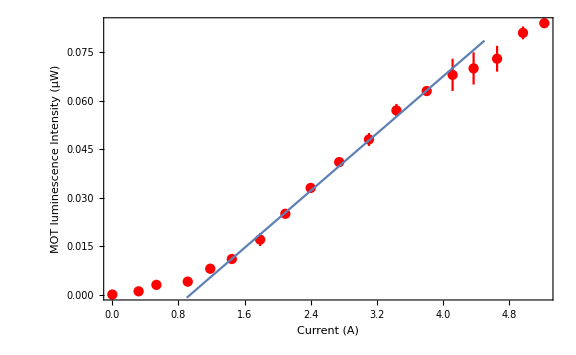

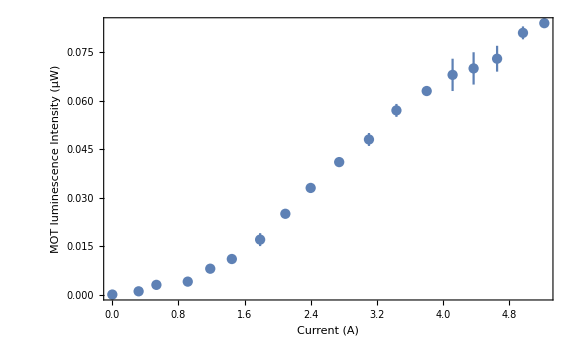

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0208856 | 0.00153539 | -13.6028 | 2.7302×10^-6
x | 0.0221113 | 0.000529295 | 41.775 | 1.17476×10^-9

```mathematica
magnet =  {{5.223,0.581, 0.001},{4.965, 0.584, 0.002},{4.652, 0.592, 0.004},{4.368,0.595,0.005},{4.114,0.597,0.005},{3.801,0.602,0.001},{3.435,0.608,0.002},{3.103,0.617,0.002},{2.743,0.624,0.001},{2.398,0.632,0.001},{2.092,0.640,0.001},{1.787,0.648,0.002},{1.445,0.654,0.001},{1.184,0.657,0.001},{0.912,0.661,0.001},{0.533,0.662,0.001},{0.318,0.664,0.001},{0.000,0.665,0.001}};
magnetError ={{#[[1]],0.665- #[[2]]},ErrorBar[#[[3]]]} &/@magnet;
lf = LinearModelFit[Map[{#[[1,1]], #[[1,2]]}&, magnetError[[5;;13]]],{1,x}, x] 
Show[ErrorListPlot[magnetError,PlotStyle->Red],  Plot[lf[x], {x, 0.9, 4.5}],Frame->{{True,False},{True,False}},FrameLabel->{Style["Current (A)",Medium],Style["MOT luminescence Intensity (μW)",Medium]}, ImageSize->Large]
Show[ErrorListPlot[magnetError],Frame->{{True,False},{True,False}},FrameLabel->{Style["Current (A)",Medium],Style["MOT luminescence Intensity (μW)",Medium]}, ImageSize->Large]
lf["ParameterTable"]
```

FittedModel[0.734944 erfc(4.94153 x-0.377655)+0.0123943]

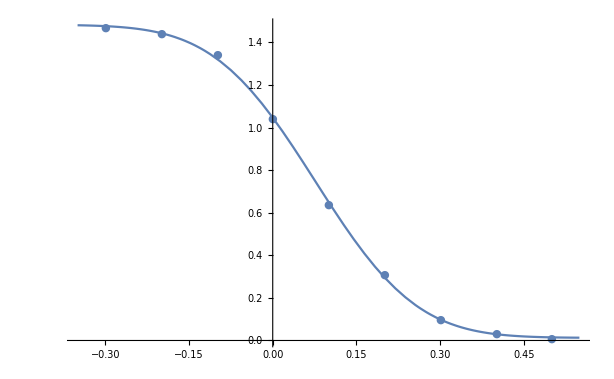

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.734944 | 0.00741214 | 99.1541 | 1.97824×10^-9
B | 4.94153 | 0.132642 | 37.2548 | 2.62451×10^-7
CC | 0.377655 | 0.0175903 | 21.4694 | 4.06591×10^-6
DD | 0.0123943 | 0.00886748 | 1.39773 | 0.221044

```mathematica
beampower = {{39.7, 1.47},{39.8, 1.44},{39.9,1.34},{40,1.04},{40.1,0.64},{40.2,0.31},{40.3,0.1},{40.4, 0.03},{40.5, 0.01}};
beampowerError = Map[{{#[[1]], #[[2]]},ErrorBar[0.01]} &,beampower];
nlm = NonlinearModelFit[Map[{#[[1]]-40,#[[2]]} &, beampower],A*Erfc[B*x-CC]+DD, {A,B,CC,DD},x]
Show[Plot[nlm[x],{x,-0.35,0.55}],ErrorListPlot[Map[{{#[[1, 1]] - 40, #[[1, 2]]},#[[2]]} &, beampowerError],PlotMarkers->{Automatic,Tiny}]]
nlm["ParameterTable"]
```

FittedModel[0.734944 erfc(4.94153 x-198.039)+0.0123943]

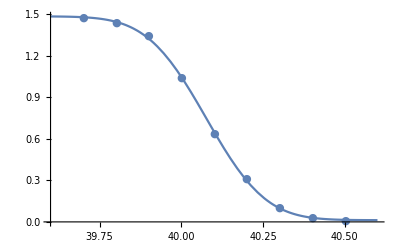

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.734944 | 0.00741214 | 99.1541 | 1.97824×10^-9
B | 4.94153 | 0.132642 | 37.2548 | 2.62451×10^-7
CC | 198.039 | 5.31686 | 37.2474 | 2.62711×10^-7
DD | 0.0123943 | 0.00886748 | 1.39773 | 0.221044

```mathematica
nlm2 = NonlinearModelFit[Map[{#[[1]],#[[2]]} &, beampower],A*Erfc[B*x-CC]+DD, {{A,0.7},{B,4.94},{CC,193.6},{DD,0.01}},x]
Show[Plot[nlm2[x],{x,39.6,40.6}],ErrorListPlot[Map[{{#[[1, 1]] , #[[1, 2]]},#[[2]]} &, beampowerError],PlotMarkers->{Automatic,Tiny}]]
nlm2["ParameterTable"]
```

FittedModel[74.8649 cos^2((π x)/180+0.791772)+605.373]

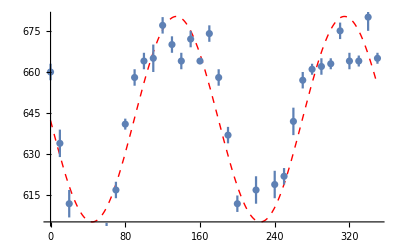

| Estimate | Standard Error | t-Statistic | P-Value
A | 74.8649 | 5.35743 | 13.974 | 2.05204×10^-15
B | -45.3652 | 2.05008 | -22.1285 | 2.27745×10^-21
CC | 605.373 | 3.28074 | 184.523 | 2.56121×10^-51

```mathematica
polarization = {{0, 660,3},{10,634,5},{20,612,5},{30,597,3},{40,589,3},{50,593,3},{60,600,5},{70,617,3},{80,641,2},{90,658,3},{100,664,3},{110,665,5},{120,677,3},{130,670,3},{140,664,3},{150,672,3},{160,664,1},{170,674,3},{180,658,3},{190,637,3},{200,612,3},{210,596,5},{220,617,5},{230,596,5},{240,619,5},{250,622,3},{260,642,5},{270,657,3},{280,661,2},{290,662,3},{300,663,2},{310,675,3},{320,664,3},{330,664,2},{340,680,5},{350,665,2}};
fit = NonlinearModelFit[Map[{#[[1]],#[[2]]}&,polarization],A*Cos[Pi*x/180-Pi*B/180]^2+CC,{{A,60},B, {CC,550}},x]
Show[Plot[fit[x],{x,0,350},PlotStyle->{Red,Thin,Dashed}],ErrorListPlot[Map[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&,polarization]]]
fit["ParameterTable"]
```